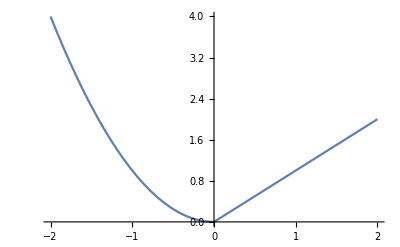

```mathematica
Plot[Piecewise[{{x^2,x<0},{x,x>0}}],{x,-2,2}]
```

Piecewise[{{0, x<0}, {9-x^2, x≤3}, {0, True}}]

Piecewise[{{9-x^2, 0≤x&&x≤3}, {0, True}}]

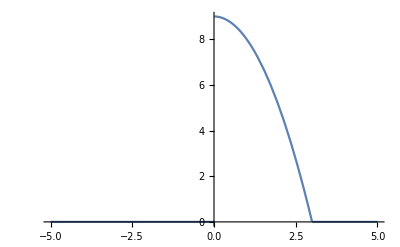

```mathematica
g=Piecewise[{{0,x<0},{9-x^2,x<=3},{0,x>3}}]
```

```mathematica
g=Piecewise[{{9-x^2,0<=x&&x<=3},{0,True}}]
Plot[g, {x,-5,5}];
A=Integrate[g,{x,-Infinity,Infinity}];
k=1/A;
f=k*g;
(*P(X<=1)*)
Integrate[f,{x,-Infinity,1}];
(*P(X<=2)*)
Integrate[f,{x,-Infinity,2}];
(*P(1<X<=2)*)
Integrate[f,{x,1,2}];
(*P(X<=x)*)
$Assumptions=x∈Reals;
F=Integrate[f,{x,-Infinity,x}]
D[F,x]
```

Piecewise[{{9-x^2, 0≤x&&x≤3}, {0, True}}]

Piecewise[{{1, x>3}, {1/54 (27 x-x^3), 0<x≤3}, {0, True}}]

Piecewise[{{0, x<0}, {1/54 (27-3 x^2), 0<x<3}, {0, x==3||x>3}, {Indeterminate, True}}]

Piecewise[{{0, x<0}, {4, x≤5}, {1, x≤11}, {0, True}}]

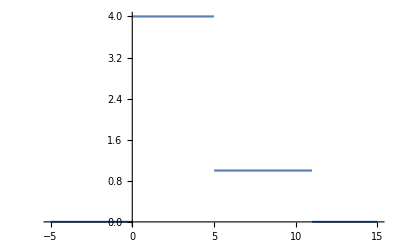

Piecewise[{{1, x>11}, {(2 x)/13, 0<x≤5}, {(15+x)/26, 5<x≤11}, {0, True}}]

49/13

3886/507

Piecewise[{{0, x<0}, {2/13, 0<x<5}, {1/26, 5<x<11}, {0, x>11}, {Indeterminate, True}}]

```mathematica
g=Piecewise[{{0,x<0},{4,x<=5},{1,x<=11},{0,True}}]
Plot[g, {x,-5,15}]
A=Integrate[g,{x,-Infinity,Infinity}];
k=1/A;
f=k*g;
(*P(X<=1)*)
Integrate[f,{x,-Infinity,1}];
(*P(X<=2)*)
Integrate[f,{x,-Infinity,2}];
(*P(1<X<=2)*)
Integrate[f,{x,1,2}];
(*P(X<=x)*)
$Assumptions=x∈Reals;
F=Integrate[f,{x,-Infinity,x}]
EV=Integrate[f*x,{x,-Infinity,Infinity}]
Var=Integrate[f*(x-EV)^2,{x,-Infinity,Infinity}]
D[F,x]
```